```mathematica
NewtonRaphson[p0_,cifras_]:=Method[{},a=N[p0];e=10^(-N[cifras]);n=0;
b=a-N[f[a]/f'[a]];error=Abs[(b-a)/b];vector={{n,a,b,f[b],error}};
While[(((f(b)>e)||(error≥ 5*e))&&n≤20),a=b;b=a-f[a]/f'[a];error=Abs[(b-a)/b];n=n+1; vector=Append[vector,{n,a,b,f[b],error}]
];Print[NumberForm[TableForm[vector,TableHeadings->{None, {"n","p{n-1}","p{n}","f(p{n})","e_r"}}],16]];];
```

```mathematica
f[x_]:= (((-1+Sin[(π*x)/2])/(-π/2 Cos[(π*x)/2])+x)((x*π)/2 Cos[(π*x)/2])+(1-Sin[(π*x)/2]))/2;
f'[x]
```

1/2 (-1/2 π Cos[(π x)/2]+1/2 π Cos[(π x)/2] (x-(2 Sec[(π x)/2] (-1+Sin[(π x)/2]))/π)-1/4 π^2 x (x-(2 Sec[(π x)/2] (-1+Sin[(π x)/2]))/π) Sin[(π x)/2]-1/2 π x (-1+Sin[(π x)/2]) Tan[(π x)/2])

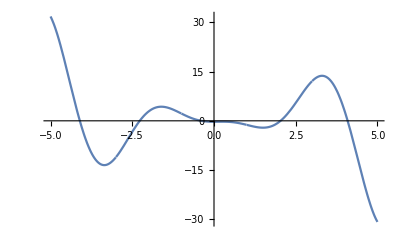

```mathematica
Plot[f'[x],{x,-5,5}]
```

```mathematica
NewtonRaphson[3,5]
```

n | p{n-1} | p{n} | f(p{n}) | e_r
0 | 3. | -3.672746374611395 | 80.6369865342956 | 1.81682743484225
1 | -3.672746374611395 | -7.837216722194114 | 0.+721.2375989328349 ⅈ | 0.531371084302085
2 | -7.837216722194114 | -5.404018937894404+0. ⅈ | 0.+186.4478213494104 ⅈ | 0.4502570794557153
3 | -5.404018937894404+0. ⅈ | -4.222037812205134-(9.05486326845283×10^-18) ⅈ | 50.58042853656316-(1.088910156335494×10^-15) ⅈ | 0.279955125525494
4 | -4.222037812205134-(9.05486326845283×10^-18) ⅈ | -4.642640799323586+(1.590841517221056×10^-17) ⅈ | 2.707604673497696×10^-15+69.25097316766833 ⅈ | 0.0905956341011203
5 | -4.642640799323586+(1.590841517221056×10^-17) ⅈ | -4.235759675570858-(1.454173869763973×10^-17) ⅈ | 48.88126945106129-(1.85453220484208×10^-15) ⅈ | 0.0960585951321454
6 | -4.235759675570858-(1.454173869763973×10^-17) ⅈ | -4.619046978811181+(2.446717424885347×10^-17) ⅈ | 4.280292142550671×10^-15+65.18132581125482 ⅈ | 0.0829797369454276
7 | -4.619046978811181+(2.446717424885347×10^-17) ⅈ | -4.246454921240806-(1.316133516047744×10^-17) ⅈ | 47.48428812141094-(1.760957202549493×10^-15) ⅈ | 0.0877419081282757
8 | -4.246454921240806-(1.316133516047744×10^-17) ⅈ | -4.601350900494454+(2.141258251825878×10^-17) ⅈ | 3.83759909714774×10^-15+62.04872679276118 ⅈ | 0.07712864915725321
9 | -4.601350900494454+(2.141258251825878×10^-17) ⅈ | -4.255138737897694-(1.296553709669221×10^-17) ⅈ | 46.29867329730167-(1.806597627270042×10^-15) ⅈ | 0.0813633077373668
10 | -4.255138737897694-(1.296553709669221×10^-17) ⅈ | -4.587413704444004+(2.052706220639184×10^-17) ⅈ | 3.759344129969434×10^-15+59.5241887519494 ⅈ | 0.07243187293625228
11 | -4.587413704444004+(2.052706220639184×10^-17) ⅈ | -4.262395115282227-(1.260109124044746×10^-17) ⅈ | 45.26969193344872-(1.818681452662718×10^-15) ⅈ | 0.0762525717046897
12 | -4.262395115282227-(1.260109124044746×10^-17) ⅈ | -4.576055057019219+(1.950151132548854×10^-17) ⅈ | 3.642206503112351×10^-15+57.42377133180164 ⅈ | 0.06854374299012602
13 | -4.576055057019219+(1.950151132548854×10^-17) ⅈ | -4.268590247974906-(1.228052338986472×10^-17) ⅈ | 44.36161192726414-(1.828320130179921×10^-15) ⅈ | 0.07202959084446663
14 | -4.268590247974906-(1.228052338986472×10^-17) ⅈ | -4.566559845252851+(1.864027034591969×10^-17) ⅈ | 3.544342585705095×10^-15+55.63462441733757 ⅈ | 0.06525034322887451
15 | -4.566559845252851+(1.864027034591969×10^-17) ⅈ | -4.273968366112137-(1.197696575045147×10^-17) ⅈ | 43.54974151690927-(1.833392555964368×10^-15) ⅈ | 0.06845897163410049
16 | -4.273968366112137-(1.197696575045147×10^-17) ⅈ | -4.558464864634614+(1.787610069930707×10^-17) ⅈ | 3.455721433135145×10^-15+54.08276858991179 ⅈ | 0.06241059369123393
17 | -4.558464864634614+(1.787610069930707×10^-17) ⅈ | -4.278700121984775-(1.16934748271353×10^-17) ⅈ | 42.81627255490551-(1.835610972958773×10^-15) ⅈ | 0.06538545228078831
18 | -4.278700121984775-(1.16934748271353×10^-17) ⅈ | -4.551454541460451+(1.719655625107823×10^-17) ⅈ | 3.375797436540577×10^-15+52.71722300793622 ⅈ | 0.05992686887039765
19 | -4.551454541460451+(1.719655625107823×10^-17) ⅈ | -4.282909195390865-(1.142845474893123×10^-17) ⅈ | 42.14792428676099-(1.835720266138958×10^-15) ⅈ | 0.06270162028151008
20 | -4.282909195390865-(1.142845474893123×10^-17) ⅈ | -4.545305190226042+(1.65870516395738×10^-17) ⅈ | 3.303171734901089×10^-15+51.5014550469887 ⅈ | 0.05772901573241277
21 | -4.545305190226042+(1.65870516395738×10^-17) ⅈ | -4.286687908735175-(1.118051344171724×10^-17) ⅈ | 41.53452145967275-(1.834285619218751×10^-15) ⅈ | 0.06033032658241138

Method[{},Null]

```mathematica
f[-3.34442];
```

```mathematica
83.52723396606567
```

83.5272

```mathematica
83.52723396606567
```

83.5272